```mathematica
Integrate[Exp[-a x^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(√a),Re[a]>0]

```mathematica
probIApp[{0,ym,ϕ},{x,y},R,sx,sl]
```

ⅇ^(-(sl^2 x^2+2 sx^2 y^2-4 sx^2 y ym+2 sx^2 ym^2-2 sl^2 x y Tan[ϕ]+2 sl^2 x ym Tan[ϕ]+(sl^2+2 sx^2) (y-ym)^2 Tan[ϕ]^2)/(sl^2 sx^2)+((-2 sl^2 x y-2 sl^2 y (-y+ym) Tan[ϕ]-4 sx^2 y (-y+ym) Tan[ϕ]-2 sl^2 x y Tan[ϕ]^2+2 (sl^2+2 sx^2) y (y-ym) Tan[ϕ]^3)^2)/(4 sl^2 sx^2 (R^2 sl^2+y (sl^2 y+2 sx^2 (y-ym))-2 sl^2 x y Tan[ϕ]+2 (R^2 sl^2+y (sx^2 (4 y-3 ym)+sl^2 (2 y-ym))) Tan[ϕ]^2-2 sl^2 x y Tan[ϕ]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 ym)) Tan[ϕ]^4)))/(2 √2 π sl sx^2 √(1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-ym))-2 sl^2 x y Tan[ϕ]+2 (R^2 sl^2+y (sx^2 (4 y-3 ym)+sl^2 (2 y-ym))) Tan[ϕ]^2-2 sl^2 x y Tan[ϕ]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 ym)) Tan[ϕ]^4)))

```mathematica
-1/(sx^2 sy^2)(sy^2 x^2+2 sx^2 y^2-4 sx^2 y ym+2 sx^2 ym^2-2 sy^2 x y Tan[ϕ]+2 sy^2 x ym Tan[ϕ]+(2 sx^2+sy^2) (y-ym)^2 Tan[ϕ]^2) //Simplify
```

-1/(sx^2 sy^2)(sy^2 x^2+2 sx^2 (y-ym)^2-2 sy^2 x (y-ym) Tan[ϕ]+(2 sx^2+sy^2) (y-ym)^2 Tan[ϕ]^2)

```mathematica
M={{1/sx^2, -Tan[ϕ]/sx^2},{-Tan[ϕ]/sx^2,2/sy^2+(2/sy^2+1/sx^2)Tan[ϕ]^2}}
```

{{1/sx^2,-Tan[ϕ]/sx^2},{-Tan[ϕ]/sx^2,2/sy^2+(1/sx^2+2/sy^2) Tan[ϕ]^2}}

```mathematica
Det[M]
```

2/(sx^2 sy^2)+(2 Tan[ϕ]^2)/(sx^2 sy^2)

```mathematica
(2 √2 π sl sx^2 √(1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-ym))-2 sl^2 x y Tan[ϕ]+2 (R^2 sl^2+y (sx^2 (4 y-3 ym)+sl^2 (2 y-ym))) Tan[ϕ]^2-2 sl^2 x y Tan[ϕ]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 ym)) Tan[ϕ]^4)))
```

2 √2 π sl sx^2 √(1/(sl^2 sx^2)(R^2 sl^2+y (sl^2 y+2 sx^2 (y-ym))-2 sl^2 x y Tan[ϕ]+2 (R^2 sl^2+y (sx^2 (4 y-3 ym)+sl^2 (2 y-ym))) Tan[ϕ]^2-2 sl^2 x y Tan[ϕ]^3+(R^2 sl^2+(sl^2+2 sx^2) y (3 y-2 ym)) Tan[ϕ]^4))

```mathematica
%//Simplify
```

2 √2 π sl sx^2 √(1/(sl^2 sx^2)Sec[ϕ]^4 (R^2 sl^2+2 sl^2 y^2+4 sx^2 y^2-sl^2 y ym-3 sx^2 y ym-y (sl^2 (y-ym)+sx^2 (2 y-ym)) Cos[2 ϕ]-sl^2 x y Sin[2 ϕ]))

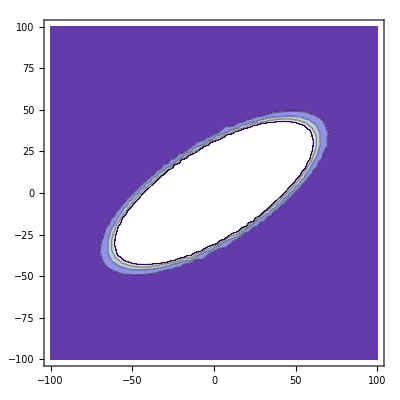

```mathematica
ContourPlot[probIApp[{0,0,Pi/4},{x,y},350,20,40],{x,-100,100},{y,-100,100}]
```

```mathematica
{{Cos,Sin},{-Sin,Cos}}.DiagonalMatrix[{A,B}].Transpose[{{Cos,Sin},{-Sin,Cos}}]
```

{{A Cos^2+B Sin^2,-A Cos Sin+B Cos Sin},{-A Cos Sin+B Cos Sin,B Cos^2+A Sin^2}}

```mathematica
Eigensystem[M]
```

{{(2 sx^2+sy^2-√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ]))/(sx^2 sy^2 (1+Cos[2 ϕ])),(2 sx^2+sy^2+√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ]))/(sx^2 sy^2 (1+Cos[2 ϕ]))},{{sx^2 Cot[ϕ] (2/sy^2-(2 sx^2+sy^2-√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ]))/(sx^2 sy^2 (1+Cos[2 ϕ]))+(1/sx^2+2/sy^2) Tan[ϕ]^2),1},{sx^2 Cot[ϕ] (2/sy^2-(2 sx^2+sy^2+√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ]))/(sx^2 sy^2 (1+Cos[2 ϕ]))+(1/sx^2+2/sy^2) Tan[ϕ]^2),1}}}

```mathematica
evec=Eigenvectors[M]//Simplify
```

{{1/(2 sy^2)(2 sx^2-sy^2 Cos[2 ϕ]+√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ])) Csc[ϕ] Sec[ϕ],1},{-1/(2 sy^2)(-2 sx^2+sy^2 Cos[2 ϕ]+√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ])) Csc[ϕ] Sec[ϕ],1}}

```mathematica
M/.{sx->20,sy->40}
```

{{1/400,-Tan[ϕ]/400},{-Tan[ϕ]/400,1/800+(3 Tan[ϕ]^2)/800}}

```mathematica
%/.ϕ->Pi/4
```

{{1/400,-1/400},{-1/400,1/200}}

```mathematica
1/Eigenvalues[2M]
```

{(sx^2 sy^2+sx^2 sy^2 Cos[2 ϕ])/(2 (2 sx^2+sy^2-√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ]))),(sx^2 sy^2+sx^2 sy^2 Cos[2 ϕ])/(2 (2 sx^2+sy^2+√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ])))}

```mathematica
Simplify[%]
```

{(sx^2 sy^2 Cos[ϕ]^2)/(2 sx^2+sy^2-√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ])),(sx^2 sy^2 Cos[ϕ]^2)/(2 sx^2+sy^2+√(4 sx^4+sy^4-4 sx^2 sy^2 Cos[2 ϕ]))}

```mathematica
%20/.{sx->Sqrt[1/4 v^2st^2],sy->Sqrt[c^2/2 st^2]}
```

{(c^2 st^4 v^2 Cos[ϕ]^2)/(8 ((c^2 st^2)/2+(st^2 v^2)/2-√((c^4 st^4)/4+(st^4 v^4)/4-1/2 c^2 st^4 v^2 Cos[2 ϕ]))),(c^2 st^4 v^2 Cos[ϕ]^2)/(8 ((c^2 st^2)/2+(st^2 v^2)/2+√((c^4 st^4)/4+(st^4 v^4)/4-1/2 c^2 st^4 v^2 Cos[2 ϕ])))}

```mathematica
%//Simplify
```

{-(c^2 st^4 v^2 Cos[ϕ]^2)/(4 (-c^2 st^2-st^2 v^2+√(st^4 (c^4+v^4-2 c^2 v^2 Cos[2 ϕ])))),(c^2 st^4 v^2 Cos[ϕ]^2)/(4 (c^2 st^2+st^2 v^2+√(st^4 (c^4+v^4-2 c^2 v^2 Cos[2 ϕ]))))}

```mathematica
%/.v->c/2
```

{-(c^4 st^4 Cos[ϕ]^2)/(16 (-5/4 c^2 st^2+√(st^4 ((17 c^4)/16-1/2 c^4 Cos[2 ϕ])))),(c^4 st^4 Cos[ϕ]^2)/(16 ((5 c^2 st^2)/4+√(st^4 ((17 c^4)/16-1/2 c^4 Cos[2 ϕ]))))}

```mathematica
%//Simplify
```

{-(c^4 st^4 Cos[ϕ]^2)/(4 (-5 c^2 st^2+√(-c^4 st^4 (-17+8 Cos[2 ϕ])))),(c^4 st^4 Cos[ϕ]^2)/(4 (5 c^2 st^2+√(-c^4 st^4 (-17+8 Cos[2 ϕ]))))}

```mathematica
Simplify[%,Assumptions->st>0 && c>0]
```

```mathematica
Sqrt[{-(c^2 st^2 Cos[ϕ]^2)/(4 (-5+√(17-8 Cos[2 ϕ]))),(c^2 st^2 Cos[ϕ]^2)/(4 (5+√(17-8 Cos[2 ϕ])))}]
```

{1/2 √(-(c^2 st^2 Cos[ϕ]^2)/(-5+√(17-8 Cos[2 ϕ]))),1/2 √((c^2 st^2 Cos[ϕ]^2)/(5+√(17-8 Cos[2 ϕ])))}

```mathematica
Simplify[%,Assumptions->st>0 && c>0]
```

{1/2 c st √(-Cos[ϕ]^2/(-5+√(17-8 Cos[2 ϕ]))),1/2 c st √(Cos[ϕ]^2/(5+√(17-8 Cos[2 ϕ])))}

```mathematica
%/.ϕ->0
```

{(c st)/(2 √2),(c st)/(4 √2)}

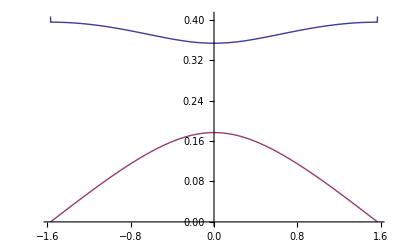

```mathematica
Plot[{1/2  √(-Cos[ϕ]^2/(-5+√(17-8 Cos[2 ϕ]))),1/2  √(Cos[ϕ]^2/(5+√(17-8 Cos[2 ϕ])))},{ϕ,-Pi/2,Pi/2}]
```